```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

```mathematica
ElecData=Import["CompareNewLimit_X10.dat"];(*Cross section has been normalised to 10^-38 cm^2*)
x=ElecData[[All,1]];(*Dark matter mass in MeV*)
sigmaElec=ElecData[[All,2]];(*Cross sec in cm^2 *)
```

```mathematica
ElecTable=Table[{x[[i]],sigmaElec[[i]] 10^-38},{i,Length[x]}];
```

```mathematica
ElecBound=Interpolation[ElecTable,InterpolationOrder->4];
```

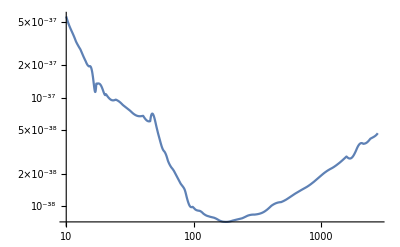

```mathematica
LogLogPlot[ElecBound[x],{x,10,2800}]
```

```mathematica
(*Calculation of Ctot *)
```

```mathematica
(************************** Definitions of Pnτ ***********************************)
Nn[R_,nn_]:=4/3 π R^3 nn
sigmaSat[R_,nn_]:=(π R^2)/Nn[R,nn]
tau[sigma_,R_,nn_]:=(3sigma)/(2sigmaSat[R,nn])
(*pn[sigma_?NumericQ,R_?NumericQ,nn_?NumericQ,N_?NumericQ]:=2/Factorial[N] NIntegrate[y Exp[-y tau[sigma,R,nn]](y tau[sigma,R,nn])^N,{y,0,1},MaxRecursion->12,WorkingPrecision->6,AccuracyGoal-> 4]*)
pn[sigma_?NumericQ,R_?NumericQ,nn_?NumericQ,N_?NumericQ]:=2/(Factorial[N] tau[sigma,R,nn]^2)(Gamma[N+2]-Gamma[N+2,tau[sigma,R,nn]])
```

```mathematica
(* Numerical Values *)
vbar=287.8 10^3(*m/sec*);
vtilde=247 10^3(*m/sec*);
ηnum=√(3/(2 vbar^2))vtilde;
ρ0=10^4(*GeV/cc*);
Tsun=3 10^17; (*sec*)
fMBboosted[u_,η_,mdm_?NumericQ]:=ρ0/mdm(3/(2 vbar^2))^(3/2)4/(√π)u^2 Exp[-3/(2 vbar^2)u^2]Exp[-η^2] Sinh[2 (√(3/(2 vbar^2))u) η]/(2(√(3/(2 vbar^2))u) η)(*x=√(3/(2 vbar^2))u*)
β[mdm_,mN_]:=(4mN mdm)/(mN+mdm)^2
gN[u_,vesc_,N_?NumericQ,mdm_?NumericQ,mN_?NumericQ]:=1/β[mdm,mN] vesc^2/(vesc^2+u^2)((1/β[mdm,mN] Log[1/(1-β[mdm,mN])])^(N-1))-(1/β[mdm,mN]-1);
umin[vesc_,N_,mdm_,mN_]:=vesc √((1/β[mdm,mN] Log[1/(1-β[mdm,mN])])^(N-1)-1)
umax[vesc_,N_?NumericQ,mdm_?NumericQ,mN_?NumericQ]:=vesc √((1/(1-β[mdm,mN])(1/β[mdm,mN] Log[1/(1-β[mdm,mN])])^(N-1))-1)
```

```mathematica
cctomtrInv=10^6;
mtrtoKm=10^-3;
```

```mathematica
CN[R_?NumericQ,σ_?NumericQ,vesc_?NumericQ,N_?NumericQ,nn_?NumericQ,mdm_?NumericQ,mN_?NumericQ]:= π R^2 pn[σ,R,nn,N]NIntegrate[gN[u,vesc,N,mdm,mN] fMBboosted[u,ηnum,mdm]/u(u^2+vesc^2),{u,umin[vesc,N,mdm,mN],umax[vesc,N,mdm,mN]},MaxRecursion->12,AccuracyGoal->10](cctomtrInv)
(* UNITS : R in mtr, u in m/sec, vesc in m/sec, mdm in GeV, ρ0 in Gev/cc, σ in m^2 *)
```

```mathematica
Nmax[R_?NumericQ,σ_?NumericQ,vesc_?NumericQ,nn_?NumericQ,mdm_?NumericQ,mn_?NumericQ]:=For[Nobj=1,Nobj≤ 10^5,Nobj++,If[Tsun CN[R,σ,vesc,Nobj,nn,mdm,mn]≤1,Return[Nobj];Break[]]];
```

```mathematica
(*CAUTION : NEEDS to get cleared from the NSUN value before Running*)
Ctot[R_?NumericQ,σ_?NumericQ,vesc_?NumericQ,nn_?NumericQ,mdm_?NumericQ,mn_?NumericQ]:=Sum[CN[R,σ,vesc,n1,nn,mdm,mn],{n1,1,Nmax[R,σ,vesc,nn,mdm,mn]}]
```

```mathematica
(* Temperature of WD and asscociated constraint *)
```

```mathematica
G=6.67408×10^-11 (*m^3 kg^-1 s^-2*);
clight=3 10^8;(*m/sec*)
σ0=5.67 10^-8(*Watt m^-2 k^-4 *);
conversionfactor=6.24 10^9;(*Joule to GeV*)
```

```mathematica
RHSofConstraint[R_,T_,M_]:=4π σ0 R^2 T^4(1-(2G M)/(R clight^2))^2 conversionfactor; (* R in mtr, T in Kelvin, M in Kg *)
```

```mathematica
RHSofConstraint[10^4,2000,1.4 2 10^30]
```

2.4322×10^24

```mathematica
plotElecWD=ListLogPlot[{Table[{x,10^x Ctot[0.07 10^8,10^-43,6 10^3,10^40,10^x,0.5 10^-3]},{x,-3,6,0.5}],Table[{x,10^x Ctot[0.07 10^8,10^-44,6 10^3,10^40,10^x,0.5 10^-3]},{x,-3,6,0.5}],Table[{x,10^x Ctot[0.07 10^8,10^-45,6 10^3,10^40,10^x,0.5 10^-3]},{x,-3,6,0.5}]},PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},PlotRange->Automatic,Frame->True,Joined-> True,AxesOrigin ->{-3,Automatic},FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["M_DMx C_Tot[GeV s^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"σ = 10^-43 m^2","σ = 10^-44 m^2","σ = 10^-45 m^2"},Top],PlotLabel->"Scattering with electrons in White Dwarf"]
```

```mathematica
(*Export["plotWD.pdf",plotElecWD];*)
```

```mathematica
(*plotElecNS=ListLogPlot[{Table[{x,10^x Ctot[10^4,10^-43,10^5,10^48,10^x,0.5 10^-3]},{x,0,4,0.3}],Table[{x,10^x Ctot[10^4,10^-44,10^5,10^48,10^x,0.5 10^-3]},{x,0,4,0.3}],Table[{x,10^x Ctot[10^4,10^-45,10^5,10^48,10^x,0.5 10^-3]},{x,0,4,0.3}]},PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},PlotRange->Automatic,Frame->True,Joined-> True,AxesOrigin ->{0,Automatic},FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["M_DMx C_Tot[GeV s^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"σ = 10^-43 m^2","σ = 10^-44 m^2","σ = 10^-45 m^2"},Top],PlotLabel->"Scattering with electrons in Neutron Star"]*)
```

```mathematica
(*Export["plotNS.pdf",plotElecNS];*)
```

```mathematica
(*plotElecWD2=ListLogPlot[{Table[{x,(1/10^33 10^x Ctot[0.07 10^8,10^-46,6 10^3,10^40,10^x,0.5 10^-3])^0.25},{x,-3,6,0.5}],Table[{x,(1/10^33 10^x Ctot[0.07 10^8,10^-48,6 10^3,10^40,10^x,0.5 10^-3])^0.25},{x,-3,6,0.5}],Table[{x,(1/10^33 10^x Ctot[0.07 10^8,10^-50,6 10^3,10^40,10^x,0.5 10^-3])^0.25},{x,-3,6,0.5}],Table[{x,1},{x,-3,6,0.5}]},PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green},{Thick,Dashed,Black}},PlotRange->Full,Frame->True,Joined-> True,AxesOrigin ->{-3,Automatic},FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["T_DM/T_obs",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"σ = 10^-46 m^2","σ = 10^-48 m^2","σ = 10^-50 m^2"},Top],PlotLabel->"Scattering with electrons in White Dwarf of 5000K (ρ_DM=10^4 GeV/cc)"]*)
```

```mathematica
(*Export["plotWD2.pdf",plotElecWD2];*)
```

```mathematica
(*cntrplot1=ListContourPlot[Table[{mdm=RandomReal[{-2,4}],xsec=RandomReal[{-45,-50}],Log10[10^mdm Ctot[0.07 10^8,10^xsec,6 10^3,10^36,10^mdm,0.5 10^-3]]},{5000}],InterpolationOrder->3,PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ] [m^2]",FontSize->20,Bold]},PlotLabel->Style["Contour plots of constant Log_10[M_DMxC_tot]",FontSize->10,Bold]]*)
```

```mathematica
(*Export["CntrplotWD1.pdf",cntrplot1];*)
```

```mathematica
(*cntrplot2=ContourPlot[10^mdm Ctot[10^4,10^xsec,10^8,10^44,10^mdm,0.5 10^-3]==1.5 10^27,{mdm,-3,4},{xsec,-49,-51},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ] [m^2]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["Contour plots of constant Log_10[M_DMC_tot] (Neutron Star)",FontSize->8,Bold]]*)
```

```mathematica
(*cntrplot2=ListContourPlot[Table[{mdm=RandomReal[{-2,4}],xsec=RandomReal[{-45,-50}],Log10[10^mdm Ctot[10^4,10^xsec,10^5,10^44,10^mdm,0.5 10^-3]]},{5000}],InterpolationOrder->3,PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ] [m^2]",FontSize->20,Bold]},PlotLabel->Style["Contour plots of constant Log_10[M_DMxC_tot] (Neutron Star)",FontSize->10,Bold]]*)
```

```mathematica
(*Export["CntrplotNS1.pdf",cntrplot2];*)
```

```mathematica
(*points=Catenate@Cases[Normal@cntrplot2,Line[pts_]->pts,Infinity];
cntrTable=Flatten/@Flatten[PadRight[points,Automatic,""],{2}];*)
```

```mathematica
(*Export["file.txt",points,"Table"];*)
```